# Stark effect with Zeeman effect

This software calculates the Stark shift of Rydberg levels in presence of a bias magnetic field, which creates also a Zeeman shift.
The magnetic field is in general not aligned with the electric field, which creates different quantization directions. So one has to include also the ΔmJ = +-1 levels with respected to the targeted level inside, as well as the ΔmJ = 0 ones (in the case without B, as the Stark interaction term couples levels with the same mL, and thus the same mJ, we could select just the levels with ΔmJ = 0).

The electric field points at the quantization direction of the atoms, the z direction; the magnetic field makes an angle α with the electric field, in the zx plane.

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 60 p3/2, mj = -1/2 >

#### Selection of Hilbert basis for the calculation, centered at |60p3/2>

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=-1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=40*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Abs[Subscript[m, A]-Subscript[m, 1]]≤ 1,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99956×10^11

{0.187,Null}

685

{{57,3,5/2,-3/2,-1.01315×10^12,-1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,7/2,-3/2,-1.01315×10^12,-1},{57,3,7/2,-1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,4,7/2,-3/2,-1.01256×10^12,1},«671»,{61,0,1/2,-1/2,-9.8239×10^11,1},{61,0,1/2,1/2,-9.8239×10^11,1},{61,1,1/2,-1/2,-9.66417×10^11,-1},{61,1,1/2,1/2,-9.66417×10^11,-1},{61,1,3/2,-3/2,-9.6598×10^11,-1},{61,1,3/2,-1/2,-9.6598×10^11,-1},{61,1,3/2,1/2,-9.6598×10^11,-1}}

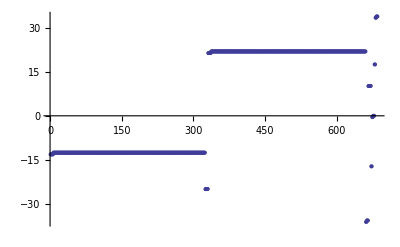

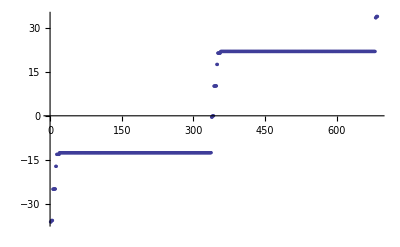

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

#### Creation of a list with the label of each level

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]
```

{59|1|1/2|-1/2,59|1|1/2|1/2,59|1|3/2|-3/2,59|1|3/2|-1/2,59|1|3/2|1/2,58|2|3/2|-3/2,58|2|3/2|-1/2,58|2|3/2|1/2,58|2|5/2|-3/2,58|2|5/2|-1/2,58|2|5/2|1/2,60|0|1/2|-1/2,60|0|1/2|1/2,57|3|7/2|-3/2,57|3|7/2|-1/2,57|3|7/2|1/2,57|3|5/2|-3/2,57|3|5/2|-1/2,57|3|5/2|1/2,57|4|7/2|-3/2,57|4|7/2|-1/2,57|4|7/2|1/2,57|4|9/2|-3/2,57|4|9/2|-1/2,57|4|9/2|1/2,57|5|9/2|-3/2,57|5|9/2|-1/2,57|5|9/2|1/2,57|5|11/2|-3/2,57|5|11/2|-1/2,57|5|11/2|1/2,57|6|11/2|-3/2,57|6|11/2|-1/2,57|6|11/2|1/2,57|6|13/2|-3/2,57|6|13/2|-1/2,57|6|13/2|1/2,57|7|13/2|-3/2,57|7|13/2|-1/2,57|7|13/2|1/2,57|7|15/2|-3/2,57|7|15/2|-1/2,57|7|15/2|1/2,57|8|15/2|-3/2,57|8|15/2|-1/2,57|8|15/2|1/2,57|8|17/2|-3/2,57|8|17/2|-1/2,57|8|17/2|1/2,57|9|17/2|-3/2,57|9|17/2|-1/2,57|9|17/2|1/2,57|9|19/2|-3/2,57|9|19/2|-1/2,57|9|19/2|1/2,57|10|19/2|-3/2,57|10|19/2|-1/2,57|10|19/2|1/2,57|10|21/2|-3/2,57|10|21/2|-1/2,57|10|21/2|1/2,57|11|21/2|-3/2,57|11|21/2|-1/2,57|11|21/2|1/2,57|11|23/2|-3/2,57|11|23/2|-1/2,57|11|23/2|1/2,57|12|23/2|-3/2,57|12|23/2|-1/2,57|12|23/2|1/2,57|12|25/2|-3/2,57|12|25/2|-1/2,57|12|25/2|1/2,57|13|25/2|-3/2,57|13|25/2|-1/2,57|13|25/2|1/2,57|13|27/2|-3/2,57|13|27/2|-1/2,57|13|27/2|1/2,57|14|27/2|-3/2,57|14|27/2|-1/2,57|14|27/2|1/2,57|14|29/2|-3/2,57|14|29/2|-1/2,57|14|29/2|1/2,57|15|29/2|-3/2,57|15|29/2|-1/2,57|15|29/2|1/2,57|15|31/2|-3/2,57|15|31/2|-1/2,57|15|31/2|1/2,57|16|31/2|-3/2,57|16|31/2|-1/2,57|16|31/2|1/2,57|16|33/2|-3/2,57|16|33/2|-1/2,57|16|33/2|1/2,57|17|33/2|-3/2,57|17|33/2|-1/2,57|17|33/2|1/2,57|17|35/2|-3/2,57|17|35/2|-1/2,57|17|35/2|1/2,57|18|35/2|-3/2,57|18|35/2|-1/2,57|18|35/2|1/2,57|18|37/2|-3/2,57|18|37/2|-1/2,57|18|37/2|1/2,57|19|37/2|-3/2,57|19|37/2|-1/2,57|19|37/2|1/2,57|19|39/2|-3/2,57|19|39/2|-1/2,57|19|39/2|1/2,57|20|39/2|-3/2,57|20|39/2|-1/2,57|20|39/2|1/2,57|20|41/2|-3/2,57|20|41/2|-1/2,57|20|41/2|1/2,57|21|41/2|-3/2,57|21|41/2|-1/2,57|21|41/2|1/2,57|21|43/2|-3/2,57|21|43/2|-1/2,57|21|43/2|1/2,57|22|43/2|-3/2,57|22|43/2|-1/2,57|22|43/2|1/2,57|22|45/2|-3/2,57|22|45/2|-1/2,57|22|45/2|1/2,57|23|45/2|-3/2,57|23|45/2|-1/2,57|23|45/2|1/2,57|23|47/2|-3/2,57|23|47/2|-1/2,57|23|47/2|1/2,57|24|47/2|-3/2,57|24|47/2|-1/2,57|24|47/2|1/2,57|24|49/2|-3/2,57|24|49/2|-1/2,57|24|49/2|1/2,57|25|49/2|-3/2,57|25|49/2|-1/2,57|25|49/2|1/2,57|25|51/2|-3/2,57|25|51/2|-1/2,57|25|51/2|1/2,57|26|51/2|-3/2,57|26|51/2|-1/2,57|26|51/2|1/2,57|26|53/2|-3/2,57|26|53/2|-1/2,57|26|53/2|1/2,57|27|53/2|-3/2,57|27|53/2|-1/2,57|27|53/2|1/2,57|27|55/2|-3/2,57|27|55/2|-1/2,57|27|55/2|1/2,57|28|55/2|-3/2,57|28|55/2|-1/2,57|28|55/2|1/2,57|28|57/2|-3/2,57|28|57/2|-1/2,57|28|57/2|1/2,57|29|57/2|-3/2,57|29|57/2|-1/2,57|29|57/2|1/2,57|29|59/2|-3/2,57|29|59/2|-1/2,57|29|59/2|1/2,57|30|59/2|-3/2,57|30|59/2|-1/2,57|30|59/2|1/2,57|30|61/2|-3/2,57|30|61/2|-1/2,57|30|61/2|1/2,57|31|61/2|-3/2,57|31|61/2|-1/2,57|31|61/2|1/2,57|31|63/2|-3/2,57|31|63/2|-1/2,57|31|63/2|1/2,57|32|63/2|-3/2,57|32|63/2|-1/2,57|32|63/2|1/2,57|32|65/2|-3/2,57|32|65/2|-1/2,57|32|65/2|1/2,57|33|65/2|-3/2,57|33|65/2|-1/2,57|33|65/2|1/2,57|33|67/2|-3/2,57|33|67/2|-1/2,57|33|67/2|1/2,57|34|67/2|-3/2,57|34|67/2|-1/2,57|34|67/2|1/2,57|34|69/2|-3/2,57|34|69/2|-1/2,57|34|69/2|1/2,57|35|69/2|-3/2,57|35|69/2|-1/2,57|35|69/2|1/2,57|35|71/2|-3/2,57|35|71/2|-1/2,57|35|71/2|1/2,57|36|71/2|-3/2,57|36|71/2|-1/2,57|36|71/2|1/2,57|36|73/2|-3/2,57|36|73/2|-1/2,57|36|73/2|1/2,57|37|73/2|-3/2,57|37|73/2|-1/2,57|37|73/2|1/2,57|37|75/2|-3/2,57|37|75/2|-1/2,57|37|75/2|1/2,57|38|75/2|-3/2,57|38|75/2|-1/2,57|38|75/2|1/2,57|38|77/2|-3/2,57|38|77/2|-1/2,57|38|77/2|1/2,57|39|77/2|-3/2,57|39|77/2|-1/2,57|39|77/2|1/2,57|39|79/2|-3/2,57|39|79/2|-1/2,57|39|79/2|1/2,57|40|79/2|-3/2,57|40|79/2|-1/2,57|40|79/2|1/2,57|40|81/2|-3/2,57|40|81/2|-1/2,57|40|81/2|1/2,57|41|81/2|-3/2,57|41|81/2|-1/2,57|41|81/2|1/2,57|41|83/2|-3/2,57|41|83/2|-1/2,57|41|83/2|1/2,57|42|83/2|-3/2,57|42|83/2|-1/2,57|42|83/2|1/2,57|42|85/2|-3/2,57|42|85/2|-1/2,57|42|85/2|1/2,57|43|85/2|-3/2,57|43|85/2|-1/2,57|43|85/2|1/2,57|43|87/2|-3/2,57|43|87/2|-1/2,57|43|87/2|1/2,57|44|87/2|-3/2,57|44|87/2|-1/2,57|44|87/2|1/2,57|44|89/2|-3/2,57|44|89/2|-1/2,57|44|89/2|1/2,57|45|89/2|-3/2,57|45|89/2|-1/2,57|45|89/2|1/2,57|45|91/2|-3/2,57|45|91/2|-1/2,57|45|91/2|1/2,57|46|91/2|-3/2,57|46|91/2|-1/2,57|46|91/2|1/2,57|46|93/2|-3/2,57|46|93/2|-1/2,57|46|93/2|1/2,57|47|93/2|-3/2,57|47|93/2|-1/2,57|47|93/2|1/2,57|47|95/2|-3/2,57|47|95/2|-1/2,57|47|95/2|1/2,57|48|95/2|-3/2,57|48|95/2|-1/2,57|48|95/2|1/2,57|48|97/2|-3/2,57|48|97/2|-1/2,57|48|97/2|1/2,57|49|97/2|-3/2,57|49|97/2|-1/2,57|49|97/2|1/2,57|49|99/2|-3/2,57|49|99/2|-1/2,57|49|99/2|1/2,57|50|99/2|-3/2,57|50|99/2|-1/2,57|50|99/2|1/2,57|50|101/2|-3/2,57|50|101/2|-1/2,57|50|101/2|1/2,57|51|101/2|-3/2,57|51|101/2|-1/2,57|51|101/2|1/2,57|51|103/2|-3/2,57|51|103/2|-1/2,57|51|103/2|1/2,57|52|103/2|-3/2,57|52|103/2|-1/2,57|52|103/2|1/2,57|52|105/2|-3/2,57|52|105/2|-1/2,57|52|105/2|1/2,57|53|105/2|-3/2,57|53|105/2|-1/2,57|53|105/2|1/2,57|53|107/2|-3/2,57|53|107/2|-1/2,57|53|107/2|1/2,57|54|107/2|-3/2,57|54|107/2|-1/2,57|54|107/2|1/2,57|54|109/2|-3/2,57|54|109/2|-1/2,57|54|109/2|1/2,57|55|109/2|-3/2,57|55|109/2|-1/2,57|55|109/2|1/2,57|55|111/2|-3/2,57|55|111/2|-1/2,57|55|111/2|1/2,57|56|111/2|-3/2,57|56|111/2|-1/2,57|56|111/2|1/2,57|56|113/2|-3/2,57|56|113/2|-1/2,57|56|113/2|1/2,60|1|1/2|-1/2,60|1|1/2|1/2,60|1|3/2|-3/2,60|1|3/2|-1/2,60|1|3/2|1/2,59|2|3/2|-3/2,59|2|3/2|-1/2,59|2|3/2|1/2,59|2|5/2|-3/2,59|2|5/2|-1/2,59|2|5/2|1/2,61|0|1/2|-1/2,61|0|1/2|1/2,58|3|7/2|-3/2,58|3|7/2|-1/2,58|3|7/2|1/2,58|3|5/2|-3/2,58|3|5/2|-1/2,58|3|5/2|1/2,58|4|7/2|-3/2,58|4|7/2|-1/2,58|4|7/2|1/2,58|4|9/2|-3/2,58|4|9/2|-1/2,58|4|9/2|1/2,58|5|9/2|-3/2,58|5|9/2|-1/2,58|5|9/2|1/2,58|5|11/2|-3/2,58|5|11/2|-1/2,58|5|11/2|1/2,58|6|11/2|-3/2,58|6|11/2|-1/2,58|6|11/2|1/2,58|6|13/2|-3/2,58|6|13/2|-1/2,58|6|13/2|1/2,58|7|13/2|-3/2,58|7|13/2|-1/2,58|7|13/2|1/2,58|7|15/2|-3/2,58|7|15/2|-1/2,58|7|15/2|1/2,58|8|15/2|-3/2,58|8|15/2|-1/2,58|8|15/2|1/2,58|8|17/2|-3/2,58|8|17/2|-1/2,58|8|17/2|1/2,58|9|17/2|-3/2,58|9|17/2|-1/2,58|9|17/2|1/2,58|9|19/2|-3/2,58|9|19/2|-1/2,58|9|19/2|1/2,58|10|19/2|-3/2,58|10|19/2|-1/2,58|10|19/2|1/2,58|10|21/2|-3/2,58|10|21/2|-1/2,58|10|21/2|1/2,58|11|21/2|-3/2,58|11|21/2|-1/2,58|11|21/2|1/2,58|11|23/2|-3/2,58|11|23/2|-1/2,58|11|23/2|1/2,58|12|23/2|-3/2,58|12|23/2|-1/2,58|12|23/2|1/2,58|12|25/2|-3/2,58|12|25/2|-1/2,58|12|25/2|1/2,58|13|25/2|-3/2,58|13|25/2|-1/2,58|13|25/2|1/2,58|13|27/2|-3/2,58|13|27/2|-1/2,58|13|27/2|1/2,58|14|27/2|-3/2,58|14|27/2|-1/2,58|14|27/2|1/2,58|14|29/2|-3/2,58|14|29/2|-1/2,58|14|29/2|1/2,58|15|29/2|-3/2,58|15|29/2|-1/2,58|15|29/2|1/2,58|15|31/2|-3/2,58|15|31/2|-1/2,58|15|31/2|1/2,58|16|31/2|-3/2,58|16|31/2|-1/2,58|16|31/2|1/2,58|16|33/2|-3/2,58|16|33/2|-1/2,58|16|33/2|1/2,58|17|33/2|-3/2,58|17|33/2|-1/2,58|17|33/2|1/2,58|17|35/2|-3/2,58|17|35/2|-1/2,58|17|35/2|1/2,58|18|35/2|-3/2,58|18|35/2|-1/2,58|18|35/2|1/2,58|18|37/2|-3/2,58|18|37/2|-1/2,58|18|37/2|1/2,58|19|37/2|-3/2,58|19|37/2|-1/2,58|19|37/2|1/2,58|19|39/2|-3/2,58|19|39/2|-1/2,58|19|39/2|1/2,58|20|39/2|-3/2,58|20|39/2|-1/2,58|20|39/2|1/2,58|20|41/2|-3/2,58|20|41/2|-1/2,58|20|41/2|1/2,58|21|41/2|-3/2,58|21|41/2|-1/2,58|21|41/2|1/2,58|21|43/2|-3/2,58|21|43/2|-1/2,58|21|43/2|1/2,58|22|43/2|-3/2,58|22|43/2|-1/2,58|22|43/2|1/2,58|22|45/2|-3/2,58|22|45/2|-1/2,58|22|45/2|1/2,58|23|45/2|-3/2,58|23|45/2|-1/2,58|23|45/2|1/2,58|23|47/2|-3/2,58|23|47/2|-1/2,58|23|47/2|1/2,58|24|47/2|-3/2,58|24|47/2|-1/2,58|24|47/2|1/2,58|24|49/2|-3/2,58|24|49/2|-1/2,58|24|49/2|1/2,58|25|49/2|-3/2,58|25|49/2|-1/2,58|25|49/2|1/2,58|25|51/2|-3/2,58|25|51/2|-1/2,58|25|51/2|1/2,58|26|51/2|-3/2,58|26|51/2|-1/2,58|26|51/2|1/2,58|26|53/2|-3/2,58|26|53/2|-1/2,58|26|53/2|1/2,58|27|53/2|-3/2,58|27|53/2|-1/2,58|27|53/2|1/2,58|27|55/2|-3/2,58|27|55/2|-1/2,58|27|55/2|1/2,58|28|55/2|-3/2,58|28|55/2|-1/2,58|28|55/2|1/2,58|28|57/2|-3/2,58|28|57/2|-1/2,58|28|57/2|1/2,58|29|57/2|-3/2,58|29|57/2|-1/2,58|29|57/2|1/2,58|29|59/2|-3/2,58|29|59/2|-1/2,58|29|59/2|1/2,58|30|59/2|-3/2,58|30|59/2|-1/2,58|30|59/2|1/2,58|30|61/2|-3/2,58|30|61/2|-1/2,58|30|61/2|1/2,58|31|61/2|-3/2,58|31|61/2|-1/2,58|31|61/2|1/2,58|31|63/2|-3/2,58|31|63/2|-1/2,58|31|63/2|1/2,58|32|63/2|-3/2,58|32|63/2|-1/2,58|32|63/2|1/2,58|32|65/2|-3/2,58|32|65/2|-1/2,58|32|65/2|1/2,58|33|65/2|-3/2,58|33|65/2|-1/2,58|33|65/2|1/2,58|33|67/2|-3/2,58|33|67/2|-1/2,58|33|67/2|1/2,58|34|67/2|-3/2,58|34|67/2|-1/2,58|34|67/2|1/2,58|34|69/2|-3/2,58|34|69/2|-1/2,58|34|69/2|1/2,58|35|69/2|-3/2,58|35|69/2|-1/2,58|35|69/2|1/2,58|35|71/2|-3/2,58|35|71/2|-1/2,58|35|71/2|1/2,58|36|71/2|-3/2,58|36|71/2|-1/2,58|36|71/2|1/2,58|36|73/2|-3/2,58|36|73/2|-1/2,58|36|73/2|1/2,58|37|73/2|-3/2,58|37|73/2|-1/2,58|37|73/2|1/2,58|37|75/2|-3/2,58|37|75/2|-1/2,58|37|75/2|1/2,58|38|75/2|-3/2,58|38|75/2|-1/2,58|38|75/2|1/2,58|38|77/2|-3/2,58|38|77/2|-1/2,58|38|77/2|1/2,58|39|77/2|-3/2,58|39|77/2|-1/2,58|39|77/2|1/2,58|39|79/2|-3/2,58|39|79/2|-1/2,58|39|79/2|1/2,58|40|79/2|-3/2,58|40|79/2|-1/2,58|40|79/2|1/2,58|40|81/2|-3/2,58|40|81/2|-1/2,58|40|81/2|1/2,58|41|81/2|-3/2,58|41|81/2|-1/2,58|41|81/2|1/2,58|41|83/2|-3/2,58|41|83/2|-1/2,58|41|83/2|1/2,58|42|83/2|-3/2,58|42|83/2|-1/2,58|42|83/2|1/2,58|42|85/2|-3/2,58|42|85/2|-1/2,58|42|85/2|1/2,58|43|85/2|-3/2,58|43|85/2|-1/2,58|43|85/2|1/2,58|43|87/2|-3/2,58|43|87/2|-1/2,58|43|87/2|1/2,58|44|87/2|-3/2,58|44|87/2|-1/2,58|44|87/2|1/2,58|44|89/2|-3/2,58|44|89/2|-1/2,58|44|89/2|1/2,58|45|89/2|-3/2,58|45|89/2|-1/2,58|45|89/2|1/2,58|45|91/2|-3/2,58|45|91/2|-1/2,58|45|91/2|1/2,58|46|91/2|-3/2,58|46|91/2|-1/2,58|46|91/2|1/2,58|46|93/2|-3/2,58|46|93/2|-1/2,58|46|93/2|1/2,58|47|93/2|-3/2,58|47|93/2|-1/2,58|47|93/2|1/2,58|47|95/2|-3/2,58|47|95/2|-1/2,58|47|95/2|1/2,58|48|95/2|-3/2,58|48|95/2|-1/2,58|48|95/2|1/2,58|48|97/2|-3/2,58|48|97/2|-1/2,58|48|97/2|1/2,58|49|97/2|-3/2,58|49|97/2|-1/2,58|49|97/2|1/2,58|49|99/2|-3/2,58|49|99/2|-1/2,58|49|99/2|1/2,58|50|99/2|-3/2,58|50|99/2|-1/2,58|50|99/2|1/2,58|50|101/2|-3/2,58|50|101/2|-1/2,58|50|101/2|1/2,58|51|101/2|-3/2,58|51|101/2|-1/2,58|51|101/2|1/2,58|51|103/2|-3/2,58|51|103/2|-1/2,58|51|103/2|1/2,58|52|103/2|-3/2,58|52|103/2|-1/2,58|52|103/2|1/2,58|52|105/2|-3/2,58|52|105/2|-1/2,58|52|105/2|1/2,58|53|105/2|-3/2,58|53|105/2|-1/2,58|53|105/2|1/2,58|53|107/2|-3/2,58|53|107/2|-1/2,58|53|107/2|1/2,58|54|107/2|-3/2,58|54|107/2|-1/2,58|54|107/2|1/2,58|54|109/2|-3/2,58|54|109/2|-1/2,58|54|109/2|1/2,58|55|109/2|-3/2,58|55|109/2|-1/2,58|55|109/2|1/2,58|55|111/2|-3/2,58|55|111/2|-1/2,58|55|111/2|1/2,58|56|111/2|-3/2,58|56|111/2|-1/2,58|56|111/2|1/2,58|56|113/2|-3/2,58|56|113/2|-1/2,58|56|113/2|1/2,58|57|113/2|-3/2,58|57|113/2|-1/2,58|57|113/2|1/2,58|57|115/2|-3/2,58|57|115/2|-1/2,58|57|115/2|1/2,61|1|1/2|-1/2,61|1|1/2|1/2,61|1|3/2|-3/2,61|1|3/2|-1/2,61|1|3/2|1/2}

#### Calculation of coupling between levels due to electric field (Stark effect)

```mathematica
(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

RDip[{1,0,1},{1,0,1}]

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]



(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

7.07037

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.27917,0.-4.27917 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, -3/2}, {1, -1}, {5/2, 3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -3/2}, {1, 1}, {5/2, 3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -3/2}, {1, -1}, {5/2, 3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -3/2}, {1, -1}, {5/2, 3/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -3/2}, {1, 1}, {5/2, 3/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -3/2}, {1, -1}, {5/2, 3/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{51.746,Null}

{0,0,0}

#### Calculation of coupling between levels due to magnetic field (Zeeman effect)

```mathematica
(*Calculation of Zeeman term <n,l,j,m| μ*B |np,lp,jp,mp> *)

Bfield = 8.71*10^(-4); (* Magnetic field in Tesla *)
α = Pi/2; (* angle between electric field and magnetic field, in radians *)

RZeeman [{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,0];
RZeeman [{60,0,1},{60,0,1}]
RZeeman [{100,0,1},{100,0,1}]
RZeeman [{60,0,1},{59,0,1}]
RZeeman [{60,1,3},{60,1,3}]
RZeeman [{60,1,3},{59,1,3}]

(*Landé g-factor*)
g[l_,j_] := 3/2+(3/4-l*(l+1))/(2*j*(j+1));

g[0,1/2]
g[1,3/2]
BMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_},α_]:=RZeeman [{np,lp,Chooselj[lp,jp]},{n,l,Chooselj[l,j]}]  *  g[lp,jp]* KroneckerDelta[lp,l]*KroneckerDelta[jp,j]* (Cos[α]*mp*KroneckerDelta[mp,m]+Sin[α]/2*(Sqrt[jp*(jp+1)-mp*(mp+1)]*KroneckerDelta[mp+1,m]+Sqrt[jp*(jp+1)-mp*(mp-1)]*KroneckerDelta[mp-1,m])  );

BMatrixelement[{60,0,1/2,1/2},{60,0,1/2,1/2},0]*Subscript[μ, B]/h/10^9*10^(-4) (*Zeeman effect, GHz per Gauss, for s fine levels *)
BMatrixelement[{60,1,3/2,3/2},{60,1,3/2,3/2},0]*Subscript[μ, B]/h/10^9*10^(-4)  (*Zeeman effect, GHz per Gauss, for p 3/2 fine levels *)



(*Fill up Matrix with  <A|μ*B|A'>  *)
Clear[AI]
BMatrix=Array[B,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[ (NList[[i,2]]==NList[[k,2]])&&(NList[[i,3]]==NList[[k,3]]) ,
BMatrix[[i,k]]=BMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]},α],
BMatrix[[i,k]]=0;]]
] 
] 

Clear[i,k,AI]

BMatrix[[1,1]]

Sin[α]
```

1.

1.

-0.000405891

1.

-0.00041805

2

4/3

0.00139962

0.00279925

{2.995,Null}

0.

1

#### Calculation of free energies for each level (without interaction): the diagonal terms of the Hamiltonian in absence of magnetic field

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.02504×10^12,-1.02504×10^12,-1.02504×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.03624×10^12,-1.03624×10^12,-1.03576×10^12,-1.03576×10^12,-1.03576×10^12,-9.89788×10^11,-9.89788×10^11,-9.89788×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-1.01724×10^12,-1.01724×10^12,-1.00042×10^12,-1.00042×10^12,-9.99956×10^11,-9.99956×10^11,-9.99956×10^11,-9.8239×10^11,-9.8239×10^11,-9.66417×10^11,-9.66417×10^11,-9.6598×10^11,-9.6598×10^11,-9.6598×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9]
```

-Graphics-

-Graphics-

-Graphics-

{-1036.25,-1036.24,-1035.78,-1035.76,-1035.73,-1025.05,-1025.04,-1025.03,-1025.01,-1024.98,-1024.95,-1017.26,-1017.23,-1013.19,-1013.17,-1013.15,-1013.15,-1013.13,-1013.11,-1013.06,-1013.06,-1013.05,-1013.05,-1013.04,-1013.04,-1013.03,-1013.03,-1013.02,-1013.02,-1013.01,-1013.01,-1013.,-1013.,-1012.99,-1012.99,-1012.99,-1012.99,-1012.98,-1012.98,-1012.97,-1012.97,-1012.96,-1012.96,-1012.95,-1012.95,-1012.94,-1012.94,-1012.93,-1012.93,-1012.92,-1012.92,-1012.92,-1012.92,-1012.91,-1012.91,-1012.9,-1012.9,-1012.89,-1012.89,-1012.88,-1012.88,-1012.87,-1012.87,-1012.86,-1012.86,-1012.86,-1012.86,-1012.85,-1012.85,-1012.84,-1012.84,-1012.83,-1012.83,-1012.82,-1012.82,-1012.81,-1012.81,-1012.8,-1012.8,-1012.79,-1012.79,-1012.79,-1012.79,-1012.78,-1012.78,-1012.77,-1012.77,-1012.76,-1012.76,-1012.75,-1012.75,-1012.74,-1012.74,-1012.73,-1012.73,-1012.73,-1012.72,-1012.72,-1012.72,-1012.71,-1012.71,-1012.7,-1012.7,-1012.69,-1012.69,-1012.68,-1012.68,-1012.67,-1012.67,-1012.66,-1012.66,-1012.65,-1012.65,-1012.64,-1012.64,-1012.63,-1012.63,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1012.5,-1012.49,-1012.49,-1012.48,-1012.48,-1012.47,-1012.47,-1012.46,-1012.46,-1012.46,-1012.45,-1012.45,-1012.44,-1012.44,-1012.43,-1012.43,-1012.42,-1012.42,-1012.41,-1012.41,-1012.4,-1012.4,-1012.39,-1012.39,-1012.39,-1012.39,-1012.38,-1012.38,-1012.37,-1012.37,-1012.36,-1012.36,-1012.35,-1012.35,-1012.34,-1012.34,-1012.33,-1012.33,-1012.33,-1012.33,-1012.32,-1012.32,-1012.31,-1012.31,-1012.3,-1012.3,-1012.29,-1012.29,-1012.28,-1012.28,-1012.27,-1012.27,-1012.26,-1012.26,-1012.26,-1012.26,-1012.25,-1012.25,-1012.24,-1012.24,-1012.23,-1012.23,-1012.22,-1012.22,-1012.21,-1012.21,-1012.2,-1012.2,-1012.2,-1012.19,-1012.19,-1012.19,-1012.18,-1012.18,-1012.17,-1012.17,-1012.16,-1012.16,-1012.15,-1012.15,-1012.14,-1012.14,-1012.13,-1012.13,-1012.13,-1012.13,-1012.12,-1012.12,-1012.11,-1012.11,-1012.1,-1012.1,-1012.09,-1012.09,-1012.08,-1012.08,-1012.07,-1012.06,-1000.42,-1000.41,-999.977,-999.956,-999.934,-989.801,-989.788,-989.775,-989.762,-989.732,-989.702,-982.402,-982.378,-978.547,-978.529,-978.508,-978.507,-978.486,-978.469,-978.458,-978.449,-978.44,-978.44,-978.432,-978.432,-978.423,-978.423,-978.414,-978.414,-978.406,-978.405,-978.397,-978.397,-978.388,-978.388,-978.38,-978.379,-978.371,-978.371,-978.362,-978.362,-978.353,-978.353,-978.345,-978.345,-978.336,-978.336,-978.327,-978.327,-978.319,-978.319,-978.31,-978.31,-978.301,-978.301,-978.293,-978.292,-978.284,-978.284,-978.275,-978.275,-978.267,-978.266,-978.258,-978.258,-978.249,-978.249,-978.24,-978.24,-978.232,-978.232,-978.223,-978.223,-978.214,-978.214,-978.206,-978.206,-978.197,-978.197,-978.188,-978.188,-978.18,-978.179,-978.171,-978.171,-978.162,-978.162,-978.154,-978.153,-978.145,-978.145,-978.136,-978.136,-978.127,-978.127,-978.119,-978.119,-978.11,-978.11,-978.101,-978.101,-978.093,-978.092,-978.084,-978.084,-978.075,-978.075,-978.067,-978.066,-978.058,-978.057,-978.049,-978.047,-978.039,-978.036,-978.029,-978.023,-978.018,-978.011,-978.011,-978.01,-978.009,-978.008,-978.006,-978.006,-978.006,-978.004,-978.004,-978.002,-978.001,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.994,-977.993,-977.992,-977.992,-977.99,-977.99,-977.987,-977.987,-977.985,-977.985,-977.983,-977.983,-977.98,-977.98,-977.978,-977.978,-977.977,-977.977,-977.976,-977.976,-977.973,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.938,-977.938,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.93,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.921,-977.92,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.905,-977.904,-977.904,-977.903,-977.902,-977.902,-977.899,-977.899,-977.897,-977.897,-977.895,-977.894,-977.892,-977.892,-977.892,-977.89,-977.89,-977.888,-977.888,-977.887,-977.88,-977.875,-977.869,-977.863,-977.859,-977.852,-977.85,-977.842,-977.841,-977.832,-977.832,-977.823,-977.823,-977.815,-977.814,-977.806,-977.806,-977.797,-977.797,-977.789,-977.788,-977.78,-977.78,-977.771,-977.771,-977.762,-977.762,-977.754,-977.754,-977.745,-977.745,-977.736,-977.736,-977.728,-977.728,-977.719,-977.719,-977.71,-977.71,-977.702,-977.701,-977.693,-977.693,-977.684,-977.684,-977.676,-977.675,-977.667,-977.667,-977.658,-977.658,-977.649,-977.649,-977.641,-977.641,-977.632,-977.632,-977.623,-977.623,-977.615,-977.615,-977.606,-977.606,-977.597,-977.597,-977.589,-977.588,-977.58,-977.58,-977.571,-977.571,-977.563,-977.562,-977.554,-977.554,-977.545,-977.545,-977.536,-977.536,-977.528,-977.528,-977.519,-977.519,-977.51,-977.51,-977.502,-977.502,-977.493,-977.493,-977.484,-977.484,-977.476,-977.475,-977.467,-977.467,-977.458,-977.458,-977.45,-977.441,-966.421,-966.413,-966.001,-965.98,-965.958}

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

{{300,-43.5899,59|1|1/2|-1/2},{300,-43.5899,59|1|1/2|1/2},{300,-40.6038,59|1|3/2|-3/2},{300,-40.6038,59|1|3/2|-1/2},{300,-40.4095,59|1|3/2|1/2},{300,-31.3163,58|2|3/2|-3/2},{300,-31.3163,58|2|3/2|-1/2},{300,-31.143,58|2|3/2|1/2},{300,-31.143,58|2|5/2|-3/2},{300,-31.1395,58|2|5/2|-1/2},{300,-30.842,58|2|5/2|1/2},{300,-30.6397,60|0|1/2|-1/2},{300,-30.6397,60|0|1/2|1/2},{300,-30.4886,57|3|7/2|-3/2},{300,-30.4886,57|3|7/2|-1/2},{300,-30.4822,57|3|7/2|1/2},{300,-30.2406,57|3|5/2|-3/2},{300,-29.9757,57|3|5/2|-1/2},{300,-29.9757,57|3|5/2|1/2},{300,-29.8408,57|4|7/2|-3/2},{300,-29.8408,57|4|7/2|-1/2},{300,-29.8319,57|4|7/2|1/2},{300,-29.7002,57|4|9/2|-3/2},{300,-29.3167,57|4|9/2|-1/2},{300,-29.3167,57|4|9/2|1/2},{300,-29.1974,57|5|9/2|-3/2},{300,-29.1974,57|5|9/2|-1/2},{300,-29.1865,57|5|9/2|1/2},{300,-29.1778,57|5|11/2|-3/2},{300,-28.6597,57|5|11/2|-1/2},{300,-28.6597,57|5|11/2|1/2},{300,-28.5994,57|6|11/2|-3/2},{300,-28.5561,57|6|11/2|-1/2},{300,-28.5561,57|6|11/2|1/2},{300,-28.544,57|6|13/2|-3/2},{300,-28.0033,57|6|13/2|-1/2},{300,-28.0033,57|6|13/2|1/2},{300,-27.9766,57|7|13/2|-3/2},{300,-27.9148,57|7|13/2|-1/2},{300,-27.9148,57|7|13/2|1/2},{300,-27.9024,57|7|15/2|-3/2},{300,-27.3466,57|7|15/2|-1/2},{300,-27.3466,57|7|15/2|1/2},{300,-27.3341,57|8|15/2|-3/2},{300,-27.272,57|8|15/2|-1/2},{300,-27.272,57|8|15/2|1/2},{300,-27.2599,57|8|17/2|-3/2},{300,-26.6893,57|8|17/2|-1/2},{300,-26.6893,57|8|17/2|1/2},{300,-26.6831,57|9|17/2|-3/2},{300,-26.6268,57|9|17/2|-1/2},{300,-26.6268,57|9|17/2|1/2},{300,-26.6154,57|9|19/2|-3/2},{300,-26.0312,57|9|19/2|-1/2},{300,-26.0312,57|9|19/2|1/2},{300,-26.0278,57|10|19/2|-3/2},{300,-25.9788,57|10|19/2|-1/2},{300,-25.9788,57|10|19/2|1/2},{300,-25.9685,57|10|21/2|-3/2},{300,-25.3722,57|10|21/2|-1/2},{300,-25.3722,57|10|21/2|1/2},{300,-25.3702,57|11|21/2|-3/2},{300,-25.3282,57|11|21/2|-1/2},{300,-25.3282,57|11|21/2|1/2},{300,-25.319,57|11|23/2|-3/2},{300,-24.7125,57|11|23/2|-1/2},{300,-24.7125,57|11|23/2|1/2},{300,-24.7112,57|12|23/2|-3/2},{300,-24.6752,57|12|23/2|-1/2},{300,-24.6752,57|12|23/2|1/2},{300,-24.6671,57|12|25/2|-3/2},{300,-24.0522,57|12|25/2|-1/2},{300,-24.0522,57|12|25/2|1/2},{300,-24.0514,57|13|25/2|-3/2},{300,-24.0202,57|13|25/2|-1/2},{300,-24.0202,57|13|25/2|1/2},{300,-24.013,57|13|27/2|-3/2},{300,-23.3913,57|13|27/2|-1/2},{300,-23.3913,57|13|27/2|1/2},{300,-23.391,57|14|27/2|-3/2},{300,-23.3635,57|14|27/2|-1/2},{300,-23.3635,57|14|27/2|1/2},{300,-23.3571,57|14|29/2|-3/2},{300,-22.7301,57|14|29/2|-1/2},{300,-22.7299,57|14|29/2|1/2},{300,-22.7299,57|15|29/2|-3/2},{300,-22.7054,57|15|29/2|-1/2},{300,-22.7054,57|15|29/2|1/2},{300,-22.6997,57|15|31/2|-3/2},{300,-22.0688,57|15|31/2|-1/2},{300,-22.0683,57|15|31/2|1/2},{300,-22.0683,57|16|31/2|-3/2},{300,-22.0461,57|16|31/2|-1/2},{300,-22.0461,57|16|31/2|1/2},{300,-22.0409,57|16|33/2|-3/2},{300,-21.4073,57|16|33/2|-1/2},{300,-21.4069,57|16|33/2|1/2},{300,-21.4069,57|17|33/2|-3/2},{300,-21.3857,57|17|33/2|-1/2},{300,-21.3857,57|17|33/2|1/2},{300,-21.381,57|17|35/2|-3/2},{300,-20.7462,57|17|35/2|-1/2},{300,-20.7462,57|17|35/2|1/2},{300,-20.7454,57|18|35/2|-3/2},{300,-20.7244,57|18|35/2|-1/2},{300,-20.7244,57|18|35/2|1/2},{300,-20.7201,57|18|37/2|-3/2},{300,-20.0889,57|18|37/2|-1/2},{300,-20.0889,57|18|37/2|1/2},{300,-20.0832,57|19|37/2|-3/2},{300,-20.0624,57|19|37/2|-1/2},{300,-20.0624,57|19|37/2|1/2},{300,-20.0583,57|19|39/2|-3/2},{300,-19.4488,57|19|39/2|-1/2},{300,-19.4488,57|19|39/2|1/2},{300,-19.4207,57|20|39/2|-3/2},{300,-19.3996,57|20|39/2|-1/2},{300,-19.3996,57|20|39/2|1/2},{300,-19.3958,57|20|41/2|-3/2},{300,-18.9906,57|20|41/2|-1/2},{300,-18.9906,57|20|41/2|1/2},{300,-18.7579,57|21|41/2|-3/2},{300,-18.736,57|21|41/2|-1/2},{300,-18.736,57|21|41/2|1/2},{300,-18.7324,57|21|43/2|-3/2},{300,-18.6618,57|21|43/2|-1/2},{300,-18.6618,57|21|43/2|1/2},{300,-18.0947,57|22|43/2|-3/2},{300,-18.0718,57|22|43/2|-1/2},{300,-18.0718,57|22|43/2|1/2},{300,-18.0684,57|22|45/2|-3/2},{300,-18.0471,57|22|45/2|-1/2},{300,-18.0471,57|22|45/2|1/2},{300,-17.4312,57|23|45/2|-3/2},{300,-17.4069,57|23|45/2|-1/2},{300,-17.4069,57|23|45/2|1/2},{300,-17.4038,57|23|47/2|-3/2},{300,-17.3912,57|23|47/2|-1/2},{300,-17.3912,57|23|47/2|1/2},{300,-16.7673,57|24|47/2|-3/2},{300,-16.7413,57|24|47/2|-1/2},{300,-16.7413,57|24|47/2|1/2},{300,-16.7385,57|24|49/2|-3/2},{300,-16.7287,57|24|49/2|-1/2},{300,-16.7287,57|24|49/2|1/2},{300,-16.103,57|25|49/2|-3/2},{300,-16.0751,57|25|49/2|-1/2},{300,-16.0751,57|25|49/2|1/2},{300,-16.0725,57|25|51/2|-3/2},{300,-16.0636,57|25|51/2|-1/2},{300,-16.0636,57|25|51/2|1/2},{300,-15.4383,57|26|51/2|-3/2},{300,-15.4082,57|26|51/2|-1/2},{300,-15.4082,57|26|51/2|1/2},{300,-15.4059,57|26|53/2|-3/2},{300,-15.397,57|26|53/2|-1/2},{300,-15.397,57|26|53/2|1/2},{300,-14.7731,57|27|53/2|-3/2},{300,-14.7407,57|27|53/2|-1/2},{300,-14.7407,57|27|53/2|1/2},{300,-14.7387,57|27|55/2|-3/2},{300,-14.7294,57|27|55/2|-1/2},{300,-14.7294,57|27|55/2|1/2},{300,-14.1074,57|28|55/2|-3/2},{300,-14.0727,57|28|55/2|-1/2},{300,-14.0727,57|28|55/2|1/2},{300,-14.0708,57|28|57/2|-3/2},{300,-14.0608,57|28|57/2|-1/2},{300,-14.0608,57|28|57/2|1/2},{300,-13.4412,57|29|57/2|-3/2},{300,-13.404,57|29|57/2|-1/2},{300,-13.404,57|29|57/2|1/2},{300,-13.4024,57|29|59/2|-3/2},{300,-13.3916,57|29|59/2|-1/2},{300,-13.3916,57|29|59/2|1/2},{300,-12.7747,57|30|59/2|-3/2},{300,-12.7349,57|30|59/2|-1/2},{300,-12.7349,57|30|59/2|1/2},{300,-12.7334,57|30|61/2|-3/2},{300,-12.7217,57|30|61/2|-1/2},{300,-12.7217,57|30|61/2|1/2},{300,-12.1078,57|31|61/2|-3/2},{300,-12.0654,57|31|61/2|-1/2},{300,-12.0654,57|31|61/2|1/2},{300,-12.064,57|31|63/2|-3/2},{300,-12.0512,57|31|63/2|-1/2},{300,-12.0512,57|31|63/2|1/2},{300,-11.4406,57|32|63/2|-3/2},{300,-11.3954,57|32|63/2|-1/2},{300,-11.3954,57|32|63/2|1/2},{300,-11.3942,57|32|65/2|-3/2},{300,-11.3803,57|32|65/2|-1/2},{300,-11.3803,57|32|65/2|1/2},{300,-10.7732,57|33|65/2|-3/2},{300,-10.7251,57|33|65/2|-1/2},{300,-10.7251,57|33|65/2|1/2},{300,-10.724,57|33|67/2|-3/2},{300,-10.7089,57|33|67/2|-1/2},{300,-10.7089,57|33|67/2|1/2},{300,-10.1054,57|34|67/2|-3/2},{300,-10.0544,57|34|67/2|-1/2},{300,-10.0544,57|34|67/2|1/2},{300,-10.0535,57|34|69/2|-3/2},{300,-10.0371,57|34|69/2|-1/2},{300,-10.0371,57|34|69/2|1/2},{300,-9.43727,57|35|69/2|-3/2},{300,-9.38345,57|35|69/2|-1/2},{300,-9.38345,57|35|69/2|1/2},{300,-9.38258,57|35|71/2|-3/2},{300,-9.36482,57|35|71/2|-1/2},{300,-9.36482,57|35|71/2|1/2},{300,-8.76885,57|36|71/2|-3/2},{300,-8.71219,57|36|71/2|-1/2},{300,-8.71219,57|36|71/2|1/2},{300,-8.71143,57|36|73/2|-3/2},{300,-8.69214,57|36|73/2|-1/2},{300,-8.69214,57|36|73/2|1/2},{300,-8.1001,57|37|73/2|-3/2},{300,-8.04076,57|37|73/2|-1/2},{300,-8.04076,57|37|73/2|1/2},{300,-8.04011,57|37|75/2|-3/2},{300,-8.01911,57|37|75/2|-1/2},{300,-8.01911,57|37|75/2|1/2},{300,-7.43103,57|38|75/2|-3/2},{300,-7.3694,57|38|75/2|-1/2},{300,-7.3694,57|38|75/2|1/2},{300,-7.36883,57|38|77/2|-3/2},{300,-7.34582,57|38|77/2|-1/2},{300,-7.34582,57|38|77/2|1/2},{300,-6.76166,57|39|77/2|-3/2},{300,-6.6986,57|39|77/2|-1/2},{300,-6.6986,57|39|77/2|1/2},{300,-6.69807,57|39|79/2|-3/2},{300,-6.67252,57|39|79/2|-1/2},{300,-6.67252,57|39|79/2|1/2},{300,-6.092,57|40|79/2|-3/2},{300,-6.02976,57|40|79/2|-1/2},{300,-6.02976,57|40|79/2|1/2},{300,-6.029,57|40|81/2|-3/2},{300,-5.99976,57|40|81/2|-1/2},{300,-5.99976,57|40|81/2|1/2},{300,-5.42208,57|41|81/2|-3/2},{300,-5.36823,57|41|81/2|-1/2},{300,-5.36823,57|41|81/2|1/2},{300,-5.36575,57|41|83/2|-3/2},{300,-5.32922,57|41|83/2|-1/2},{300,-5.32922,57|41|83/2|1/2},{300,-4.75724,57|42|83/2|-3/2},{300,-4.75724,57|42|83/2|-1/2},{300,-4.75194,57|42|83/2|1/2},{300,-4.73402,57|42|85/2|-3/2},{300,-4.66907,57|42|85/2|-1/2},{300,-4.66907,57|42|85/2|1/2},{300,-4.42505,57|43|85/2|-3/2},{300,-4.42505,57|43|85/2|-1/2},{300,-4.32659,57|43|85/2|1/2},{300,-4.12027,57|43|87/2|-3/2},{300,-4.12027,57|43|87/2|-1/2},{300,-4.08151,57|43|87/2|1/2},{300,-3.93763,57|44|87/2|-3/2},{300,-3.93763,57|44|87/2|-1/2},{300,-3.91386,57|44|87/2|1/2},{300,-3.83974,57|44|89/2|-3/2},{300,-3.83974,57|44|89/2|-1/2},{300,-3.41094,57|44|89/2|1/2},{300,-3.28714,57|45|89/2|-3/2},{300,-3.28714,57|45|89/2|-1/2},{300,-3.27976,57|45|89/2|1/2},{300,-3.25072,57|45|91/2|-3/2},{300,-3.25072,57|45|91/2|-1/2},{300,-2.7402,57|45|91/2|1/2},{300,-2.61821,57|46|91/2|-3/2},{300,-2.61821,57|46|91/2|-1/2},{300,-2.61405,57|46|91/2|1/2},{300,-2.5854,57|46|93/2|-3/2},{300,-2.5854,57|46|93/2|-1/2},{300,-2.06933,57|46|93/2|1/2},{300,-1.94444,57|47|93/2|-3/2},{300,-1.94444,57|47|93/2|-1/2},{300,-1.94148,57|47|93/2|1/2},{300,-1.91067,57|47|95/2|-3/2},{300,-1.91067,57|47|95/2|-1/2},{300,-1.39837,57|47|95/2|1/2},{300,-1.26837,57|48|95/2|-3/2},{300,-1.26837,57|48|95/2|-1/2},{300,-1.26601,57|48|95/2|1/2},{300,-1.23258,57|48|97/2|-3/2},{300,-1.23258,57|48|97/2|-1/2},{300,-0.727379,57|48|97/2|1/2},{300,-0.590739,57|49|97/2|-3/2},{300,-0.590739,57|49|97/2|-1/2},{300,-0.588739,57|49|97/2|1/2},{300,-0.552432,57|49|99/2|-3/2},{300,-0.552432,57|49|99/2|-1/2},{300,-0.0563956,57|49|99/2|1/2},{300,0.088204,57|50|99/2|-3/2},{300,0.088204,57|50|99/2|-1/2},{300,0.0899611,57|50|99/2|1/2},{300,0.129455,57|50|101/2|-3/2},{300,0.129455,57|50|101/2|-1/2},{300,0.614508,57|50|101/2|1/2},{300,0.768439,57|51|101/2|-3/2},{300,0.768439,57|51|101/2|-1/2},{300,0.770021,57|51|101/2|1/2},{300,0.813115,57|51|103/2|-3/2},{300,0.813115,57|51|103/2|-1/2},{300,1.28525,57|51|103/2|1/2},{300,1.45008,57|52|103/2|-3/2},{300,1.45008,57|52|103/2|-1/2},{300,1.45153,57|52|103/2|1/2},{300,1.49879,57|52|105/2|-3/2},{300,1.49879,57|52|105/2|-1/2},{300,1.95572,57|52|105/2|1/2},{300,2.13337,57|53|105/2|-3/2},{300,2.13337,57|53|105/2|-1/2},{300,2.13471,57|53|105/2|1/2},{300,2.18695,57|53|107/2|-3/2},{300,2.18695,57|53|107/2|-1/2},{300,2.62575,57|53|107/2|1/2},{300,2.8187,57|54|107/2|-3/2},{300,2.8187,57|54|107/2|-1/2},{300,2.81996,57|54|107/2|1/2},{300,2.8783,57|54|109/2|-3/2},{300,2.8783,57|54|109/2|-1/2},{300,3.29511,57|54|109/2|1/2},{300,3.50634,57|55|109/2|-3/2},{300,3.50634,57|55|109/2|-1/2},{300,3.50759,57|55|109/2|1/2},{300,3.57123,57|55|111/2|-3/2},{300,3.57123,57|55|111/2|-1/2},{300,3.72814,57|55|111/2|1/2},{300,3.72814,57|56|111/2|-3/2},{300,3.84285,57|56|111/2|-1/2},{300,3.84285,57|56|111/2|1/2},{300,3.84393,57|56|113/2|-3/2},{300,3.96304,57|56|113/2|-1/2},{300,4.12174,57|56|113/2|1/2},{300,4.19995,60|1|1/2|-1/2},{300,4.19995,60|1|1/2|1/2},{300,4.20097,60|1|3/2|-3/2},{300,4.27805,60|1|3/2|-1/2},{300,4.27805,60|1|3/2|1/2},{300,4.45453,59|2|3/2|-3/2},{300,4.45453,59|2|3/2|-1/2},{300,4.54026,59|2|3/2|1/2},{300,4.54026,59|2|5/2|-3/2},{300,4.54208,59|2|5/2|-1/2},{300,4.62978,59|2|5/2|1/2},{300,4.76586,61|0|1/2|-1/2},{300,4.90177,61|0|1/2|1/2},{300,4.90177,58|3|7/2|-3/2},{300,4.90245,58|3|7/2|-1/2},{300,5.00487,58|3|7/2|1/2},{300,5.00487,58|3|5/2|-3/2},{300,5.16122,58|3|5/2|-1/2},{300,5.16122,58|3|5/2|1/2},{300,5.22986,58|4|7/2|-3/2},{300,5.22986,58|4|7/2|-1/2},{300,5.23238,58|4|7/2|1/2},{300,5.38418,58|4|9/2|-3/2},{300,5.84617,58|4|9/2|-1/2},{300,5.84617,58|4|9/2|1/2},{300,5.91024,58|5|9/2|-3/2},{300,5.91024,58|5|9/2|-1/2},{300,5.91383,58|5|9/2|1/2},{300,5.97342,58|5|11/2|-3/2},{300,6.52847,58|5|11/2|-1/2},{300,6.52847,58|5|11/2|1/2},{300,6.55147,58|6|11/2|-3/2},{300,6.5859,58|6|11/2|-1/2},{300,6.5859,58|6|11/2|1/2},{300,6.59057,58|6|13/2|-3/2},{300,7.15083,58|6|13/2|-1/2},{300,7.20457,58|6|13/2|1/2},{300,7.20457,58|7|13/2|-3/2},{300,7.2565,58|7|13/2|-1/2},{300,7.2565,58|7|13/2|1/2},{300,7.26233,58|7|15/2|-3/2},{300,7.77935,58|7|15/2|-1/2},{300,7.87497,58|7|15/2|1/2},{300,7.87497,58|8|15/2|-3/2},{300,7.92224,58|8|15/2|-1/2},{300,7.92224,58|8|15/2|1/2},{300,7.92927,58|8|17/2|-3/2},{300,8.42784,58|8|17/2|-1/2},{300,8.54041,58|8|17/2|1/2},{300,8.54041,58|9|17/2|-3/2},{300,8.58357,58|9|17/2|-1/2},{300,8.58357,58|9|17/2|1/2},{300,8.59175,58|9|19/2|-3/2},{300,9.08783,58|9|19/2|-1/2},{300,9.20192,58|9|19/2|1/2},{300,9.20192,58|10|19/2|-3/2},{300,9.24141,58|10|19/2|-1/2},{300,9.24141,58|10|19/2|1/2},{300,9.25053,58|10|21/2|-3/2},{300,9.75443,58|10|21/2|-1/2},{300,9.86095,58|10|21/2|1/2},{300,9.86095,58|11|21/2|-3/2},{300,9.89716,58|11|21/2|-1/2},{300,9.89716,58|11|21/2|1/2},{300,9.90684,58|11|23/2|-3/2},{300,10.425,58|11|23/2|-1/2},{300,10.5191,58|11|23/2|1/2},{300,10.5191,58|12|23/2|-3/2},{300,10.5525,58|12|23/2|-1/2},{300,10.5525,58|12|23/2|1/2},{300,10.5623,58|12|25/2|-3/2},{300,11.0982,58|12|25/2|-1/2},{300,11.1781,58|12|25/2|1/2},{300,11.1781,58|13|25/2|-3/2},{300,11.209,58|13|25/2|-1/2},{300,11.209,58|13|25/2|1/2},{300,11.2185,58|13|27/2|-3/2},{300,11.773,58|13|27/2|-1/2},{300,11.8388,58|13|27/2|1/2},{300,11.8388,58|14|27/2|-3/2},{300,11.8678,58|14|27/2|-1/2},{300,11.8678,58|14|27/2|1/2},{300,11.8768,58|14|29/2|-3/2},{300,12.4489,58|14|29/2|-1/2},{300,12.502,58|14|29/2|1/2},{300,12.502,58|15|29/2|-3/2},{300,12.5297,58|15|29/2|-1/2},{300,12.5297,58|15|29/2|1/2},{300,12.5378,58|15|31/2|-3/2},{300,13.1256,58|15|31/2|-1/2},{300,13.1676,58|15|31/2|1/2},{300,13.1676,58|16|31/2|-3/2},{300,13.1946,58|16|31/2|-1/2},{300,13.1946,58|16|31/2|1/2},{300,13.2019,58|16|33/2|-3/2},{300,13.8029,58|16|33/2|-1/2},{300,13.8352,58|16|33/2|1/2},{300,13.8352,58|17|33/2|-3/2},{300,13.8623,58|17|33/2|-1/2},{300,13.8623,58|17|33/2|1/2},{300,13.8689,58|17|35/2|-3/2},{300,14.4806,58|17|35/2|-1/2},{300,14.5043,58|17|35/2|1/2},{300,14.5043,58|18|35/2|-3/2},{300,14.5326,58|18|35/2|-1/2},{300,14.5326,58|18|35/2|1/2},{300,14.5384,58|18|37/2|-3/2},{300,15.1585,58|18|37/2|-1/2},{300,15.1738,58|18|37/2|1/2},{300,15.1738,58|19|37/2|-3/2},{300,15.2049,58|19|37/2|-1/2},{300,15.2049,58|19|37/2|1/2},{300,15.2102,58|19|39/2|-3/2},{300,15.8367,58|19|39/2|-1/2},{300,15.8418,58|19|39/2|1/2},{300,15.8418,58|20|39/2|-3/2},{300,15.879,58|20|39/2|-1/2},{300,15.879,58|20|39/2|1/2},{300,15.8837,58|20|41/2|-3/2},{300,16.503,58|20|41/2|-1/2},{300,16.503,58|20|41/2|1/2},{300,16.5149,58|21|41/2|-3/2},{300,16.5545,58|21|41/2|-1/2},{300,16.5545,58|21|41/2|1/2},{300,16.5587,58|21|43/2|-3/2},{300,17.1373,58|21|43/2|-1/2},{300,17.1373,58|21|43/2|1/2},{300,17.1932,58|22|43/2|-3/2},{300,17.231,58|22|43/2|-1/2},{300,17.231,58|22|43/2|1/2},{300,17.2349,58|22|45/2|-3/2},{300,17.6461,58|22|45/2|-1/2},{300,17.6461,58|22|45/2|1/2},{300,17.8714,58|23|45/2|-3/2},{300,17.9084,58|23|45/2|-1/2},{300,17.9084,58|23|45/2|1/2},{300,17.912,58|23|47/2|-3/2},{300,18.0617,58|23|47/2|-1/2},{300,18.0617,58|23|47/2|1/2},{300,18.5497,58|24|47/2|-3/2},{300,18.5866,58|24|47/2|-1/2},{300,18.5866,58|24|47/2|1/2},{300,18.5898,58|24|49/2|-3/2},{300,18.6495,58|24|49/2|-1/2},{300,18.6495,58|24|49/2|1/2},{300,19.2279,58|25|49/2|-3/2},{300,19.2652,58|25|49/2|-1/2},{300,19.2652,58|25|49/2|1/2},{300,19.2681,58|25|51/2|-3/2},{300,19.3036,58|25|51/2|-1/2},{300,19.3036,58|25|51/2|1/2},{300,19.906,58|26|51/2|-3/2},{300,19.9443,58|26|51/2|-1/2},{300,19.9443,58|26|51/2|1/2},{300,19.947,58|26|53/2|-3/2},{300,19.973,58|26|53/2|-1/2},{300,19.973,58|26|53/2|1/2},{300,20.5841,58|27|53/2|-3/2},{300,20.6237,58|27|53/2|-1/2},{300,20.6237,58|27|53/2|1/2},{300,20.6262,58|27|55/2|-3/2},{300,20.6477,58|27|55/2|-1/2},{300,20.6477,58|27|55/2|1/2},{300,21.2622,58|28|55/2|-3/2},{300,21.3035,58|28|55/2|-1/2},{300,21.3035,58|28|55/2|1/2},{300,21.3058,58|28|57/2|-3/2},{300,21.3251,58|28|57/2|-1/2},{300,21.3251,58|28|57/2|1/2},{300,21.9401,58|29|57/2|-3/2},{300,21.9834,58|29|57/2|-1/2},{300,21.9834,58|29|57/2|1/2},{300,21.9856,58|29|59/2|-3/2},{300,22.0039,58|29|59/2|-1/2},{300,22.0039,58|29|59/2|1/2},{300,22.618,58|30|59/2|-3/2},{300,22.6635,58|30|59/2|-1/2},{300,22.6635,58|30|59/2|1/2},{300,22.6656,58|30|61/2|-3/2},{300,22.6835,58|30|61/2|-1/2},{300,22.6835,58|30|61/2|1/2},{300,23.2957,58|31|61/2|-3/2},{300,23.3436,58|31|61/2|-1/2},{300,23.3436,58|31|61/2|1/2},{300,23.3456,58|31|63/2|-3/2},{300,23.3637,58|31|63/2|-1/2},{300,23.3637,58|31|63/2|1/2},{300,23.9732,58|32|63/2|-3/2},{300,24.0237,58|32|63/2|-1/2},{300,24.0237,58|32|63/2|1/2},{300,24.0256,58|32|65/2|-3/2},{300,24.0442,58|32|65/2|-1/2},{300,24.0442,58|32|65/2|1/2},{300,24.6504,58|33|65/2|-3/2},{300,24.7037,58|33|65/2|-1/2},{300,24.7037,58|33|65/2|1/2},{300,24.7055,58|33|67/2|-3/2},{300,24.7249,58|33|67/2|-1/2},{300,24.7249,58|33|67/2|1/2},{300,25.3273,58|34|67/2|-3/2},{300,25.3836,58|34|67/2|-1/2},{300,25.3836,58|34|67/2|1/2},{300,25.3854,58|34|69/2|-3/2},{300,25.4057,58|34|69/2|-1/2},{300,25.4057,58|34|69/2|1/2},{300,26.0039,58|35|69/2|-3/2},{300,26.0633,58|35|69/2|-1/2},{300,26.0633,58|35|69/2|1/2},{300,26.0651,58|35|71/2|-3/2},{300,26.0866,58|35|71/2|-1/2},{300,26.0866,58|35|71/2|1/2},{300,26.6803,58|36|71/2|-3/2},{300,26.7429,58|36|71/2|-1/2},{300,26.7429,58|36|71/2|1/2},{300,26.7447,58|36|73/2|-3/2},{300,26.7675,58|36|73/2|-1/2},{300,26.7675,58|36|73/2|1/2},{300,27.3565,58|37|73/2|-3/2},{300,27.4224,58|37|73/2|-1/2},{300,27.4224,58|37|73/2|1/2},{300,27.4241,58|37|75/2|-3/2},{300,27.4484,58|37|75/2|-1/2},{300,27.4484,58|37|75/2|1/2},{300,28.0325,58|38|75/2|-3/2},{300,28.1017,58|38|75/2|-1/2},{300,28.1017,58|38|75/2|1/2},{300,28.1035,58|38|77/2|-3/2},{300,28.1295,58|38|77/2|-1/2},{300,28.1295,58|38|77/2|1/2},{300,28.7083,58|39|77/2|-3/2},{300,28.7809,58|39|77/2|-1/2},{300,28.7809,58|39|77/2|1/2},{300,28.7828,58|39|79/2|-3/2},{300,28.8107,58|39|79/2|-1/2},{300,28.8107,58|39|79/2|1/2},{300,29.384,58|40|79/2|-3/2},{300,29.4599,58|40|79/2|-1/2},{300,29.4599,58|40|79/2|1/2},{300,29.462,58|40|81/2|-3/2},{300,29.4921,58|40|81/2|-1/2},{300,29.4921,58|40|81/2|1/2},{300,30.0595,58|41|81/2|-3/2},{300,30.1387,58|41|81/2|-1/2},{300,30.1387,58|41|81/2|1/2},{300,30.1409,58|41|83/2|-3/2},{300,30.1736,58|41|83/2|-1/2},{300,30.1736,58|41|83/2|1/2},{300,30.7349,58|42|83/2|-3/2},{300,30.8169,58|42|83/2|-1/2},{300,30.8169,58|42|83/2|1/2},{300,30.8195,58|42|85/2|-3/2},{300,30.8553,58|42|85/2|-1/2},{300,30.8553,58|42|85/2|1/2},{300,31.4102,58|43|85/2|-3/2},{300,31.4944,58|43|85/2|-1/2},{300,31.4944,58|43|85/2|1/2},{300,31.4975,58|43|87/2|-3/2},{300,31.5372,58|43|87/2|-1/2},{300,31.5372,58|43|87/2|1/2},{300,32.0853,58|44|87/2|-3/2},{300,32.1704,58|44|87/2|-1/2},{300,32.1704,58|44|87/2|1/2},{300,32.1746,58|44|89/2|-3/2},{300,32.2194,58|44|89/2|-1/2},{300,32.2194,58|44|89/2|1/2},{300,32.7604,58|45|89/2|-3/2},{300,32.8433,58|45|89/2|-1/2},{300,32.8433,58|45|89/2|1/2},{300,32.8494,58|45|91/2|-3/2},{300,32.902,58|45|91/2|-1/2},{300,32.902,58|45|91/2|1/2},{300,33.4353,58|46|91/2|-3/2},{300,33.5079,58|46|91/2|-1/2},{300,33.5079,58|46|91/2|1/2},{300,33.519,58|46|93/2|-3/2},{300,33.5848,58|46|93/2|-1/2},{300,33.5848,58|46|93/2|1/2},{300,34.1102,58|47|93/2|-3/2},{300,34.1436,58|47|93/2|-1/2},{300,34.1436,58|47|93/2|1/2},{300,34.1719,58|47|95/2|-3/2},{300,34.2681,58|47|95/2|-1/2},{300,34.2681,58|47|95/2|1/2},{300,34.6578,58|48|95/2|-3/2},{300,34.6578,58|48|95/2|-1/2},{300,34.7496,58|48|95/2|1/2},{300,34.785,58|48|97/2|-3/2},{300,34.9517,58|48|97/2|-1/2},{300,34.9517,58|48|97/2|1/2},{300,35.0871,58|49|97/2|-3/2},{300,35.0871,58|49|97/2|-1/2},{300,35.1639,58|49|97/2|1/2},{300,35.4597,58|49|99/2|-3/2},{300,35.6355,58|49|99/2|-1/2},{300,35.6355,58|49|99/2|1/2},{300,35.6767,58|50|99/2|-3/2},{300,35.6767,58|50|99/2|-1/2},{300,35.6941,58|50|99/2|1/2},{300,36.1343,58|50|101/2|-3/2},{300,36.3192,58|50|101/2|-1/2},{300,36.3192,58|50|101/2|1/2},{300,36.3332,58|51|101/2|-3/2},{300,36.3332,58|51|101/2|-1/2},{300,36.3381,58|51|101/2|1/2},{300,36.8087,58|51|103/2|-3/2},{300,37.0017,58|51|103/2|-1/2},{300,37.0017,58|51|103/2|1/2},{300,37.0067,58|52|103/2|-3/2},{300,37.0067,58|52|103/2|-1/2},{300,37.0083,58|52|103/2|1/2},{300,37.4829,58|52|105/2|-3/2},{300,37.6809,58|52|105/2|-1/2},{300,37.6809,58|52|105/2|1/2},{300,37.6864,58|53|105/2|-3/2},{300,37.6864,58|53|105/2|-1/2},{300,37.6871,58|53|105/2|1/2},{300,38.1568,58|53|107/2|-3/2},{300,38.3453,58|53|107/2|-1/2},{300,38.3453,58|53|107/2|1/2},{300,38.3699,58|54|107/2|-3/2},{300,38.3699,58|54|107/2|-1/2},{300,38.3704,58|54|107/2|1/2},{300,38.8303,58|54|109/2|-3/2},{300,38.9303,58|54|109/2|-1/2},{300,38.9303,58|54|109/2|1/2},{300,39.0567,58|55|109/2|-3/2},{300,39.0567,58|55|109/2|-1/2},{300,39.057,58|55|109/2|1/2},{300,39.3432,58|55|111/2|-3/2},{300,39.3432,58|55|111/2|-1/2},{300,39.5031,58|55|111/2|1/2},{300,39.7467,58|56|111/2|-3/2},{300,39.7467,58|56|111/2|-1/2},{300,39.7469,58|56|111/2|1/2},{300,39.8944,58|56|113/2|-3/2},{300,39.8944,58|56|113/2|-1/2},{300,40.1751,58|56|113/2|1/2},{300,40.4404,58|57|113/2|-3/2},{300,40.4404,58|57|113/2|-1/2},{300,40.4405,58|57|113/2|1/2},{300,40.5664,58|57|115/2|-3/2},{300,40.5664,58|57|115/2|-1/2},{300,40.8458,58|57|115/2|1/2},{300,41.1394,61|1|1/2|-1/2},{300,41.1394,61|1|1/2|1/2},{300,41.1395,61|1|3/2|-3/2},{300,41.2793,61|1|3/2|-1/2},{300,41.2793,61|1|3/2|1/2}}

-Graphics-

-Graphics-

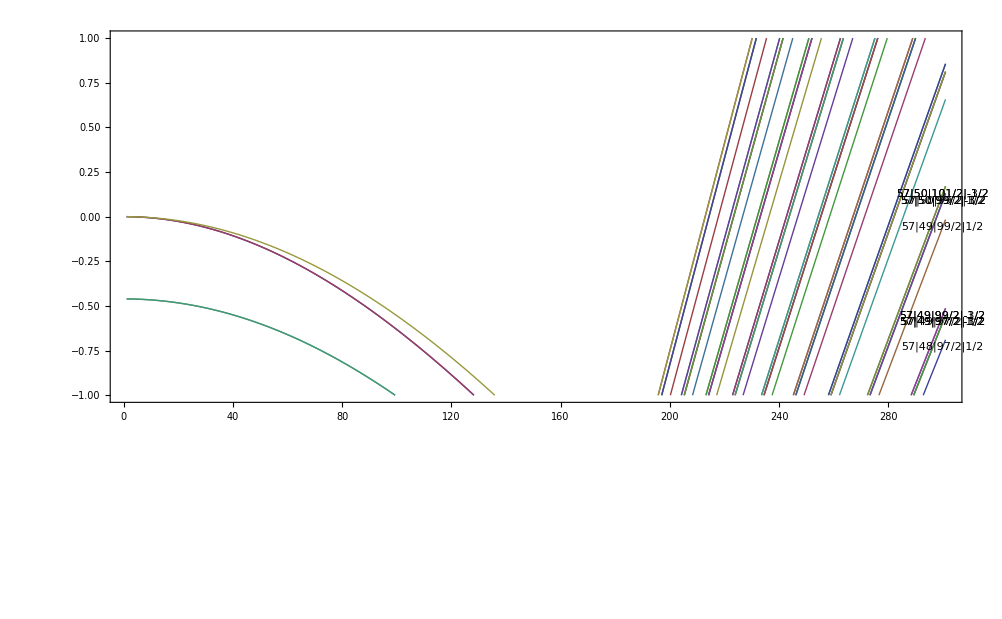

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[218]]

MPList[[218]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=Re[MPList[[i,j,2]]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60p3_2_mj1_2_with_B.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60p3_2_mj1_2.dat",Efieldlist]

(*Export["60p_j3_2_mj3_2_stark_Shift.dat",MPList[[218]]]*)
```

57|37|73/2|-3/2

{{1,-12.5928},{2,-12.5769},{3,-12.5609},{4,-12.5449},{5,-12.5289-1.84723×10^-13 ⅈ},{6,-12.5128},{7,-12.4967+2.40093×10^-13 ⅈ},{8,-12.4806+8.49861×10^-14 ⅈ},{9,-12.4644},{10,-12.4482},{11,-12.432},{12,-12.4158-2.65013×10^-13 ⅈ},{13,-12.3996},{14,-12.3834},{15,-12.3671},{16,-12.3509},{17,-12.3346},{18,-12.3183+1.71415×10^-13 ⅈ},{19,-12.302},{20,-12.2857},{21,-12.2695},{22,-12.2532},{23,-12.2369},{24,-12.2206},{25,-12.2043},{26,-12.188},{27,-12.1717},{28,-12.1554},{29,-12.1392},{30,-12.1229},{31,-12.1066},{32,-12.0904},{33,-12.0741},{34,-12.0579},{35,-12.0416},{36,-12.0254},{37,-12.0091},{38,-11.9929},{39,-11.9767},{40,-11.9605},{41,-11.9443+1.433×10^-15 ⅈ},{42,-11.9281},{43,-11.9119},{44,-11.8957},{45,-11.8795},{46,-11.8634},{47,-11.8472},{48,-11.8311},{49,-11.8149},{50,-11.7988},{51,-11.7827},{52,-11.7666},{53,-11.7505},{54,-11.7344},{55,-11.7183},{56,-11.7023},{57,-11.6862},{58,-11.6701},{59,-11.6541},{60,-11.6381},{61,-11.622},{62,-11.606},{63,-11.59+3.86765×10^-13 ⅈ},{64,-11.574},{65,-11.5581},{66,-11.5421},{67,-11.5261},{68,-11.5102},{69,-11.4942},{70,-11.4783},{71,-11.4624},{72,-11.4465},{73,-11.4306},{74,-11.4147},{75,-11.3988},{76,-11.3829-9.36124×10^-14 ⅈ},{77,-11.3671},{78,-11.3512},{79,-11.3354},{80,-11.3196},{81,-11.3037},{82,-11.2879-1.57258×10^-13 ⅈ},{83,-11.2721},{84,-11.2563},{85,-11.2406},{86,-11.2248},{87,-11.2091},{88,-11.1933},{89,-11.1776},{90,-11.1619},{91,-11.1461},{92,-11.1304},{93,-11.1148},{94,-11.0991},{95,-11.0834},{96,-11.0678},{97,-11.0521},{98,-11.0365},{99,-11.0208},{100,-11.0052},{101,-10.9896},{102,-10.974},{103,-10.9585},{104,-10.9429},{105,-10.9273},{106,-10.9118},{107,-10.8962},{108,-10.8807},{109,-10.8652},{110,-10.8497+2.84466×10^-13 ⅈ},{111,-10.8342},{112,-10.8187},{113,-10.8032},{114,-10.7878},{115,-10.7723},{116,-10.7569},{117,-10.7414-1.13436×10^-13 ⅈ},{118,-10.726},{119,-10.7106},{120,-10.6952},{121,-10.6798},{122,-10.6645},{123,-10.6491},{124,-10.6337},{125,-10.6184},{126,-10.6031},{127,-10.5877},{128,-10.5724},{129,-10.5571},{130,-10.5418},{131,-10.5266-5.96305×10^-13 ⅈ},{132,-10.5113},{133,-10.496},{134,-10.4808},{135,-10.4655},{136,-10.4503+2.62815×10^-13 ⅈ},{137,-10.4351},{138,-10.4199},{139,-10.4047},{140,-10.3895},{141,-10.3744},{142,-10.3592-5.93435×10^-14 ⅈ},{143,-10.3441},{144,-10.3289},{145,-10.3138},{146,-10.2987},{147,-10.2836},{148,-10.2685},{149,-10.2534},{150,-10.2383},{151,-10.2233},{152,-10.2082-4.71543×10^-14 ⅈ},{153,-10.1932+1.53162×10^-13 ⅈ},{154,-10.1782},{155,-10.1631-1.03773×10^-13 ⅈ},{156,-10.1481},{157,-10.1331-1.36624×10^-14 ⅈ},{158,-10.1182},{159,-10.1032},{160,-10.0882},{161,-10.0733-5.96601×10^-14 ⅈ},{162,-10.0583},{163,-10.0434},{164,-10.0285},{165,-10.0136},{166,-9.99867},{167,-9.98378},{168,-9.96891},{169,-9.95404},{170,-9.93919+2.83482×10^-13 ⅈ},{171,-9.92435},{172,-9.90952},{173,-9.89469},{174,-9.87988},{175,-9.86509},{176,-9.8503},{177,-9.83552},{178,-9.82075},{179,-9.806},{180,-9.79125-4.32534×10^-14 ⅈ},{181,-9.77652},{182,-9.76179},{183,-9.74708-3.29472×10^-13 ⅈ},{184,-9.73238},{185,-9.71769},{186,-9.70301},{187,-9.68834},{188,-9.67368},{189,-9.65903},{190,-9.6444},{191,-9.62977},{192,-9.61516+4.50586×10^-14 ⅈ},{193,-9.60055},{194,-9.58596-2.28706×10^-13 ⅈ},{195,-9.57138},{196,-9.55681},{197,-9.54225},{198,-9.5277},{199,-9.51316},{200,-9.49863},{201,-9.48411},{202,-9.46961},{203,-9.45511},{204,-9.44062},{205,-9.42615},{206,-9.41169},{207,-9.39723},{208,-9.38279},{209,-9.36836},{210,-9.35394},{211,-9.33953+3.28608×10^-13 ⅈ},{212,-9.32513},{213,-9.31075},{214,-9.29637},{215,-9.282},{216,-9.26765},{217,-9.2533},{218,-9.23897},{219,-9.22465},{220,-9.21034},{221,-9.19603},{222,-9.18174},{223,-9.16746},{224,-9.15319},{225,-9.13894},{226,-9.12469-9.67413×10^-14 ⅈ},{227,-9.11045-1.72425×10^-13 ⅈ},{228,-9.09623+1.53267×10^-13 ⅈ},{229,-9.08201},{230,-9.06781},{231,-9.05361},{232,-9.03943},{233,-9.02526},{234,-9.0111},{235,-8.99694},{236,-8.9828},{237,-8.96868},{238,-8.95456},{239,-8.94045},{240,-8.92635},{241,-8.91227},{242,-8.89819},{243,-8.88413},{244,-8.87007},{245,-8.85603},{246,-8.842},{247,-8.82797},{248,-8.81396},{249,-8.79996},{250,-8.78597},{251,-8.77199},{252,-8.75802},{253,-8.74407},{254,-8.73012},{255,-8.71618+6.07997×10^-14 ⅈ},{256,-8.70226},{257,-8.68834},{258,-8.67444},{259,-8.66054},{260,-8.64666},{261,-8.63279},{262,-8.61893+1.51423×10^-13 ⅈ},{263,-8.60508},{264,-8.59124},{265,-8.57741},{266,-8.56359},{267,-8.54978+4.96245×10^-15 ⅈ},{268,-8.53598},{269,-8.5222},{270,-8.50842},{271,-8.49466+1.63478×10^-13 ⅈ},{272,-8.4809},{273,-8.46716},{274,-8.45342},{275,-8.4397+1.52694×10^-13 ⅈ},{276,-8.42599},{277,-8.41229},{278,-8.3986},{279,-8.38492},{280,-8.37125},{281,-8.35759},{282,-8.34394+2.27354×10^-13 ⅈ},{283,-8.3303},{284,-8.31668},{285,-8.30306},{286,-8.28945},{287,-8.27586},{288,-8.26228},{289,-8.2487},{290,-8.23514},{291,-8.22159},{292,-8.20805},{293,-8.19452+9.33795×10^-16 ⅈ},{294,-8.18099},{295,-8.16749},{296,-8.15399},{297,-8.1405},{298,-8.12702},{299,-8.11355},{300,-8.1001},{301,-8.08665}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-36.2864,-36.2866,-36.287,-36.2875,-36.2881,-36.2889,-36.2899-2.2646×10^-26 ⅈ,-36.2909,-36.2922,-36.2935,-36.295,-36.2967,-36.2985,«276»,-43.1736-2.14776×10^-31 ⅈ,-43.2149,-43.2563,-43.2978-1.02442×10^-31 ⅈ,-43.3393,-43.3809,-43.4226,-43.4643,-43.5061,-43.548,-43.5899,-43.6319},«683»,{«1»}}

Stark_Shifts_around_60p3_2_mj1_2_with_B.dat

Electric_fields_for_Stark_Shifts_around_60p3_2_mj1_2.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat

## Old data

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

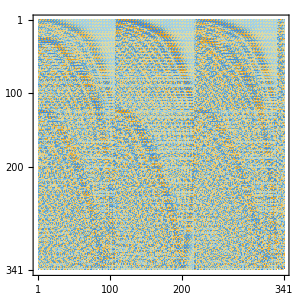

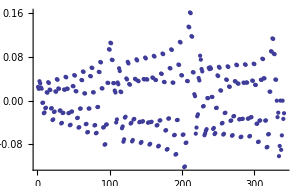

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

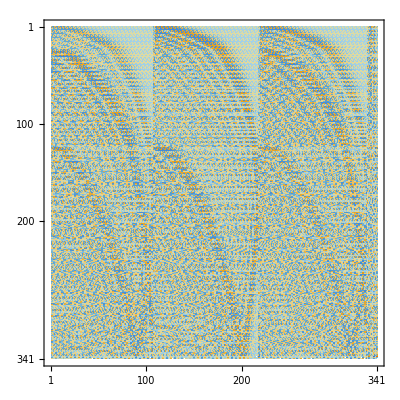

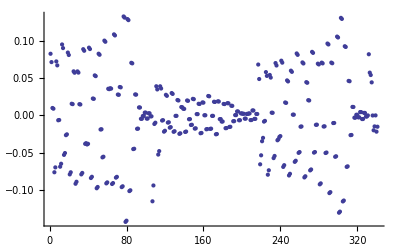

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```